# Pyr conv rates

```mathematica
myAxesSize=15;
myLabelSize=12;
myImageSize=500;
```

Case 1 - u(x,y,z) = x^2

### Pts extracted from pz

```mathematica
neq={96,704,2304,5376,10400,17856};
h1={0.0549425,0.015023,0.00716338,0.00428266,0.00289409,0.00211095};
l2={0.0501596,0.0124746,0.00553585,0.00311179,0.00199075,0.0013821};
semih1={0.0224207,0.00837112,0.00454626,0.00294244,0.00210064,0.00159559};
ptsh1=Table[{neq[[i]],h1[[i]]},{i,Length[neq]}];
ptsl2=Table[{neq[[i]],l2[[i]]},{i,Length[neq]}];
ptssemih1=Table[{neq[[i]],semih1[[i]]},{i,Length[neq]}];
```

### Plots

```mathematica
ListLogLogPlot[{ptsh1,ptsl2,ptssemih1},PlotRange->All,PlotStyle->Thickness[0.003],ImageSize->myImageSize 1.5,PlotLabel->Style["h-convergence  LogLog Plot",14,Black],AxesLabel->{Style["ndofs",myAxesSize,Black],Style["e_r",myAxesSize,Black]},LabelStyle->Directive[myLabelSize,Bold,Black],Joined->True,PlotMarkers->Automatic,PlotLegends->Placed[{"H1","L2","Semi-H1"},{0.75,0.85}]]
```

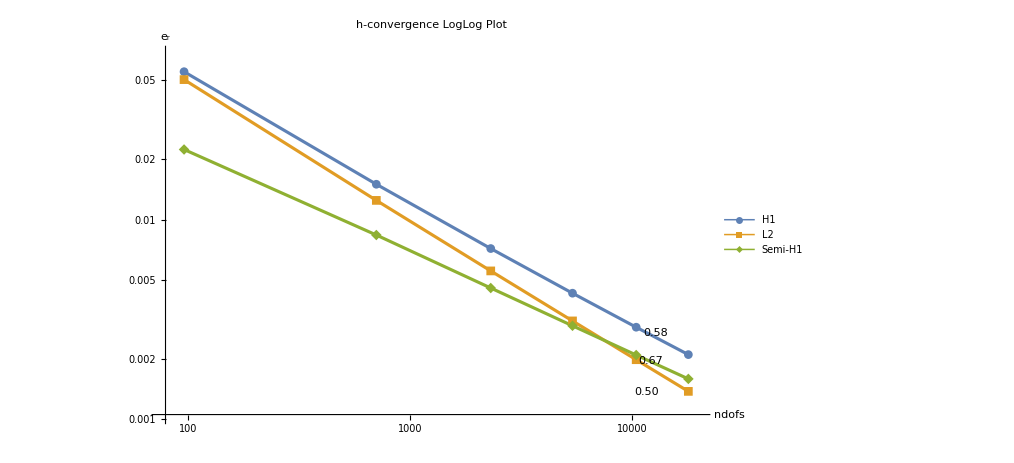

### Conv rates

```mathematica
convratesh1=Range[Length[neq]-1];
convratesl2=Range[Length[neq]-1];
convratesh1semi=Range[Length[neq]-1];
For[i=1,i≤Length[neq]-1,i++,
convratesh1[[i]]=Log[h1[[i]]/h1[[i+1]]]/Log[neq[[i]]/neq[[i+1]]];
convratesl2[[i]]=Log[l2[[i]]/l2[[i+1]]]/Log[neq[[i]]/neq[[i+1]]];
convratesh1semi[[i]]=Log[semih1[[i]]/semih1[[i+1]]]/Log[neq[[i]]/neq[[i+1]]];
]
convratesh1
convratesl2
convratesh1semi
```

{-0.650816,-0.624651,-0.607115,-0.593918,-0.583743}

{-0.698401,-0.685251,-0.679864,-0.67694,-0.675087}

{-0.49447,-0.514904,-0.513474,-0.510709,-0.508754}